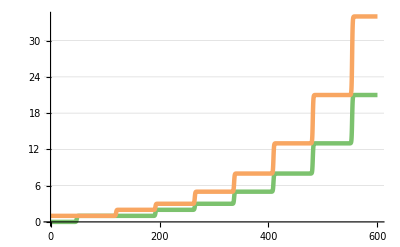

```mathematica
Get[NotebookDirectory[]<>"fibonacci.m"];

rsys=FibonacciRsys[];
tmax=600;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
PlotForPaper[Evaluate[{f0[t],f1[t]}/.sol], tmax]
```